# Steady state analysis cooperativity+berg

```mathematica
RangeΦ=Range[0,1,0.1];
```

```mathematica
X[J_,μ_]:=1/2(J+μ);
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√(Sinh[X[J,μ]]^2+Exp[-J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√(Sinh[X[J,μ]]^2+Exp[-J]));
ξ[J_,μ_] := Log[λp[J,μ]/λm[J,μ]]^-1;
```

## Average occupation

```mathematica
Φ[J_,μ_,Nm_]:= 1/2(1 + Tanh[Nm/(2ξ[J,μ])] Sinh[X[J,μ]]/(√(Sinh[X[J,μ]]^2+ Exp[-J])) );
```

```mathematica
Φ[0.00000001,-0.81,13]*13
```

4.00258

## Standard deviation

```mathematica
Φ2[J_,μ_,Nm_]:= 1/4(1 + Sinh[X[J,μ]]^2/(Sinh[X[J,μ]]^2+Exp[-J])+Tanh[Nm/(2ξ[J,μ])]((2Sinh[X[J,μ]])/(√(Sinh[X[J,μ]]^2+Exp[-J]))+1/Nm (Exp[-J]Cosh[X[J,μ]])/((Sinh[X[J,μ]]^2+Exp[-J])^(3/2))));
σ2[J_,μ_,Nm_] := Φ2[J,μ,Nm]-Φ[J,μ,Nm]^2;
σ[J_,μ_,Nm_]:=√(Φ2[J,μ,Nm]-Φ[J,μ,Nm]^2);
```

## Data from simulations

```mathematica
Data3CB0 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=0_a= 3.06_Res.dat"];
Data6CB0 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=0_a= 6.15_Res.dat"];
Data30CB0 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=0_a=30.44_Res.dat"];
Data3CB1 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=1_a= 3.06_Res.dat"];
Data6CB1 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=1_a= 6.15_Res.dat"];
Data30CB1 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=1_a=30.44_Res.dat"];
Data3CB2 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=2_a= 3.06_Res.dat"];
Data6CB2 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=2_a= 6.15_Res.dat"];
Data30CB2 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=2_a=30.44_Res.dat"];
Data3CB3 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=3_a= 3.06_Res.dat"];
Data6CB3 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=3_a= 6.15_Res.dat"];
Data30CB3 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=3_a=30.44_Res.dat"];
Data3CB4 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=4_a= 3.06_Res.dat"];
Data6CB4 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=4_a= 6.15_Res.dat"];Data30CB4 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Equilibrium_analysis/sdt_vs_Nss_J=4_a=30.44_Res.dat"];
```

```mathematica
Data3CBJ0= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=0.00  _mu=-0.81 _a= 3.06.dat"];
Data6CBJ0= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=0.00  _mu=-0.81 _a= 6.15.dat"];
Data30CBJ0= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=0.00  _mu=-0.81 _a=30.44.dat"];
Data3CBJ1= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=1.00  _mu=-1.50 _a= 3.06.dat"];
Data6CBJ1= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=1.00  _mu=-1.50 _a= 6.15.dat"];
Data30CBJ1= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=1.00  _mu=-1.50 _a=30.44.dat"];
Data3CBJ2= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=2.00  _mu=-2.30 _a= 3.06.dat"];
Data6CBJ2= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=2.00  _mu=-2.30 _a= 6.15.dat"];
Data30CBJ2= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=2.00  _mu=-2.30 _a=30.44.dat"];
Data3CBJ3= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=3.00  _mu=-3.18 _a= 3.06.dat"];
Data6CBJ3= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=3.00  _mu=-3.18 _a= 6.15.dat"];
Data30CBJ3= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=3.00  _mu=-3.18 _a=30.44.dat"];
Data3CBJ4= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=4.00  _mu=-4.12 _a= 3.06.dat"];
Data6CBJ4= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=4.00  _mu=-4.12 _a= 6.15.dat"];
Data30CBJ4= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=4.00  _mu=-4.12 _a=30.44.dat"];
```

```mathematica
Data3CBJ08= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=0.00  _mu= 0.47 _a= 3.06.dat"];
Data6CBJ08= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=0.00  _mu= 0.47 _a= 6.15.dat"];
Data30CBJ08= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=0.00  _mu= 0.47 _a=30.44.dat"];
Data3CBJ18= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=1.00  _mu=-0.71 _a= 3.06.dat"];
Data6CBJ18= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=1.00  _mu=-0.71 _a= 6.15.dat"];
Data30CBJ18= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=1.00  _mu=-0.71 _a=30.44.dat"];
Data3CBJ28= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=2.00  _mu=-1.83 _a= 3.06.dat"];
Data6CBJ28= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=2.00  _mu=-1.83 _a= 6.15.dat"];
Data30CBJ28= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=2.00  _mu=-1.83 _a=30.44.dat"];
Data3CBJ38= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=3.00  _mu=-2.89 _a= 3.06.dat"];
Data6CBJ38= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=3.00  _mu=-2.89 _a= 6.15.dat"];
Data30CBJ38= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=3.00  _mu=-2.89 _a=30.44.dat"];
Data3CBJ48= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=4.00  _mu=-3.93 _a= 3.06.dat"];
Data6CBJ48= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=4.00  _mu=-3.93 _a= 6.15.dat"];
Data30CBJ48= Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/Berg_CoopKMC/Av_KMC_Coop_Berg_J=4.00  _mu=-3.93 _a=30.44.dat"];
```

## Plots

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

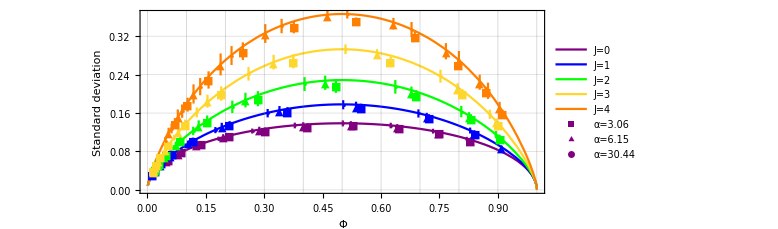

```mathematica
Show[ParametricPlot[Evaluate[Table[{Φ[J,μ,13],σ[J,μ,13]},{J,0.000001,5}]],{μ,-7,7},PlotRange->Full,Frame->True,GridLines->{RangeΦ,Automatic},FrameLabel->{"Φ","Standard deviation"}, PlotLegends->LineLegend[{"J=0","J=1", "J=2","J=3","J=4"},LegendFunction->Framed],PlotStyle->{Purple,Blue,Green,RGBColor[1,0.84,0.17],Orange},ImageSize->Large,LabelStyle->{GrayLevel[0],12}],ErrorListPlot[{Data3CB0[[All,{3,4,5}]]/13,Data6CB0[[All,{3,4,5}]]/13,Data30CB0[[All,{3,4,5}]]/13,Data3CB1[[All,{3,4,5}]]/13,Data6CB1[[All,{3,4,5}]]/13,Data30CB1[[All,{3,4,5}]]/13,Data3CB2[[All,{3,4,5}]]/13,Data6CB2[[All,{3,4,5}]]/13,Data30CB2[[All,{3,4,5}]]/13,Data3CB3[[All,{3,4,5}]]/13,Data6CB3[[All,{3,4,5}]]/13,Data30CB3[[All,{3,4,5}]]/13,Data3CB4[[All,{3,4,5}]]/13,Data6CB4[[All,{3,4,5}]]/13,Data30CB4[[All,{3,4,5}]]/13},PlotMarkers->{Style["■",Purple],Style["▲",Purple],Style["•",Purple],Style["■",Blue],Style["▲",Blue],Style["•",Blue],Style["■",Green],Style["▲",Green],Style["•",Green],Style["■",RGBColor[1,0.84,0.17]],Style["▲",RGBColor[1,0.84,0.17]],Style["•",RGBColor[1,0.84,0.17]],Style["■",Orange],Style["▲",Orange],Style["•",Orange]},PlotStyle->{Purple,Purple,Purple,Blue,Blue,Blue,Green,Green,Green,RGBColor[1,0.84,0.17],RGBColor[1,0.84,0.17],RGBColor[1,0.84,0.17],Orange,Orange,Orange},PlotLegends->LineLegend[{"α=3.06","α=6.15","α=30.44"},LegendFunction->Framed]]]
```

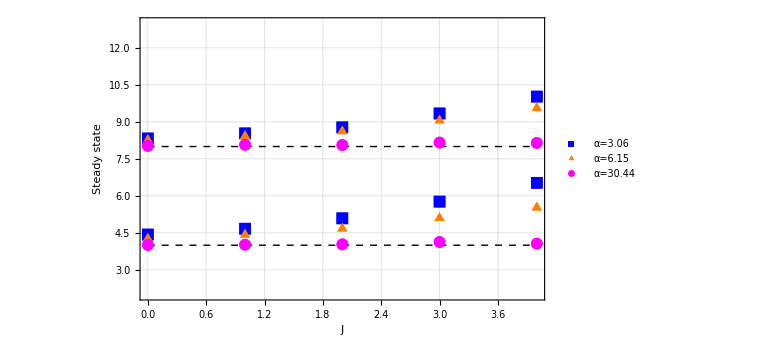

```mathematica
Show[ListPlot[{Data3CBJ0[[All,{1,2}]],Data6CBJ0[[All,{1,2}]],Data30CBJ0[[All,{1,2}]],Data3CBJ1[[All,{1,2}]],Data6CBJ1[[All,{1,2}]],Data30CBJ1[[All,{1,2}]],Data3CBJ2[[All,{1,2}]],Data6CBJ2[[All,{1,2}]],Data30CBJ2[[All,{1,2}]],Data3CBJ3[[All,{1,2}]],Data6CBJ3[[All,{1,2}]],Data30CBJ3[[All,{1,2}]],Data3CBJ4[[All,{1,2}]],Data6CBJ4[[All,{1,2}]],Data30CBJ4[[All,{1,2}]],Data3CBJ08[[All,{1,2}]],Data6CBJ08[[All,{1,2}]],Data30CBJ08[[All,{1,2}]],Data3CBJ18[[All,{1,2}]],Data6CBJ18[[All,{1,2}]],Data30CBJ18[[All,{1,2}]],Data3CBJ28[[All,{1,2}]],Data6CBJ28[[All,{1,2}]],Data30CBJ28[[All,{1,2}]],Data3CBJ38[[All,{1,2}]],Data6CBJ38[[All,{1,2}]],Data30CBJ38[[All,{1,2}]],Data3CBJ48[[All,{1,2}]],Data6CBJ48[[All,{1,2}]],Data30CBJ48[[All,{1,2}]]},PlotRange->{2,13},Frame->True,PlotMarkers->{Style["■",Blue,12],Style["▲",Orange,12],Style["•",Magenta,12]},PlotStyle->{{
Blue},{Orange},{Magenta}},GridLines->Automatic,PlotLegends->Placed[LineLegend[{"α=3.06","α=6.15","α=30.44"},LegendFunction->Framed],{{0.2,0.7},{0.8,0.0}}],FrameLabel->{"J", "Steady state"},LabelStyle->Directive[GrayLevel[0],12],ImageSize->Large], Graphics[{Dashed,Line [{{0,4},{4,4}}]}],Graphics[{Dashed,Line [{{0,8},{4,8}}]}]]
```